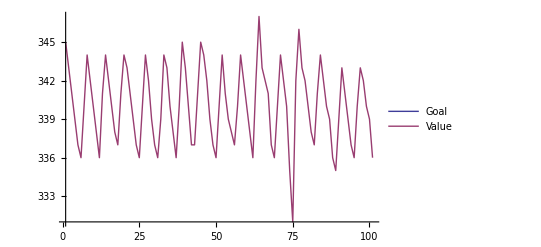

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["data.txt","Table"];
data=data[[2;;]];
data=Transpose[Transpose[data][[1;;2]]];
ListLinePlot[{(*Transpose[data][[1]][[200;;300]]*),Transpose[data][[2]][[250;;350]]},PlotRange->{All},PlotLegends->{"Goal","Value"}]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | -3.43739 | 0.240863 | -14.2711 | 1.44986×10^-25
o | 340.072 | 0.171056 | 1988.08 | 2.07665×10^-225
p | 1.58543 | 0.143521 | 11.0467 | 7.5014×10^-19
ω | 0.987003 | 0.0024458 | 403.551 | 3.02936×10^-158

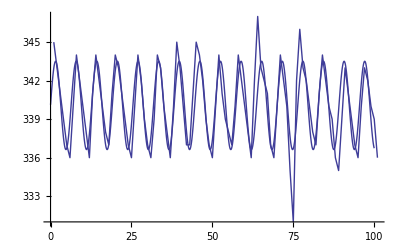

```mathematica
fitdata=Transpose[data][[2]][[250;;350]];
nlm=NonlinearModelFit[fitdata,a*Cos[t*ω+p]+o,{a,o,p,ω},t];
nlm["ParameterTable"]
Show[ListLinePlot[fitdata],Plot[nlm[t],{t,0,100}]]
```